4.)

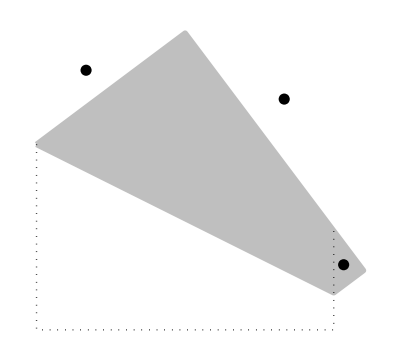

```mathematica
Graphics[
{
EdgeForm[Thickness[0.01]],White,
Triangle[{{-1,1},{-.5,1},{-1,5/8}}],
Triangle[{{-.5,1},{0,1},{0,1/3}}],
EdgeForm[Thickness[0.01]], GrayLevel[0.75],Polygon[{{-1,5/8},{0,1/8},{1/10,1/5},{-.5,1}}],
Black,Thick,Dotted,Line[{{-1,5/8},{-1,0},{0,0},{0,1/3}}],
PointSize[0.02],Point[{{-1/6,7/9},{-5/6,7/8},{1/30,79/360}}]
}
]
```

5.)

```mathematica
Manipulate[
Graphics[{
GrayLevel[0.35],EdgeForm[{Thickness[0.007],Black}],
Disk[{0,m n},m n,{Pi/2,3Pi/2}],
Disk[{(m^2-n^2)/2,0},(m^2-n^2)/2,{Pi,2Pi}],

White,
Disk[{(m^2-n^2)/2,m n},(m^2+n^2)/2,{Pi-ArcTan[2m n/(m^2-n^2)],2Pi -ArcTan[2m n/(m^2-n^2)]}],

GrayLevel[0.75],EdgeForm[Thickness[0.008]], 
Triangle[{
{0,0},{m^2-n^2,0},{0,2m n}
}]

}],
{{m,18},1,20,1,Appearance->"Labeled"},
{{n,5},1,20,1,Appearance->"Labeled"}
]
```

6.)

```mathematica
ParametricPlot[
Table[
{
{x,Sin[x]+n},
{Sin[x]+n,x}
},
{n,-10,10,.25}
],
{x,-8Pi,8Pi},
PlotRange->{{-11,11},{-11,11}},
AspectRatio->1,
Axes->False,
PlotStyle->{Black},
ImageSize->Large
]
```

-Graphics-